De acuerdo a las ecuaciones (11) y (12) de Amarilla 2018

```mathematica
Δ[r_,M_,a_]:=r^2-2M*r+a^2
ξ[r_,M_,a_]:=((r^2-a^2)*M-r*Δ[r,M,a])/(a*(r-M))
η[r_,M_,a_]:=(r^3*(4*M*Δ[r,M,a]-r*(r-M)^2))/(a^2*(r-M)^2)
α[r_,M_,a_,θ_]:=-ξ[r,M,a]*Csc[θ]
β[r_,M_,a_,θ_]:=√(η[r,M,a]+(a*Cos[θ])^2-(ξ[r,M,a]*Cot[θ])^2)
```

Luego la sombra es:

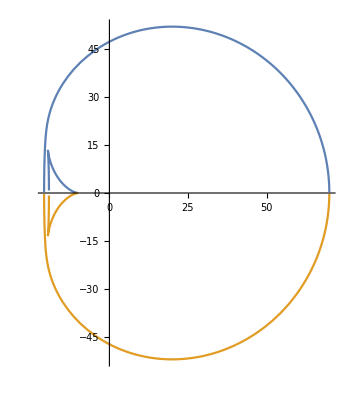

```mathematica
M=10;
a=9.99;
ParametricPlot[{{α[r,M,a,π/2],β[r,M,a,π/2]},{α[r,M,a,π/2],-β[r,M,a,π/2]}},{r,0,5M}]
```